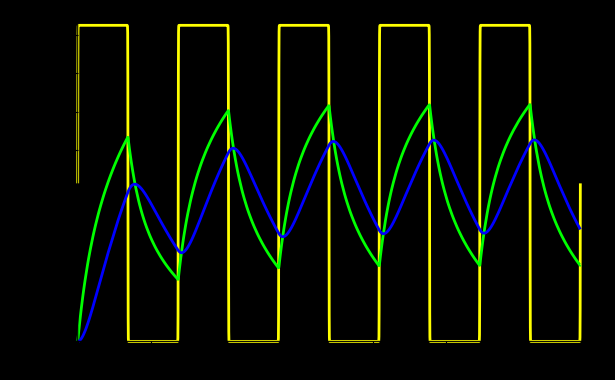

```mathematica
ClearAll["Global`*"];
suciastky={r1->10000,r2->10000,r3->1000000,c1->33*10^-9,c2->22*10^-9};
amp=3.3;
f=917;
tmax=5*1/f;
uz[t_]:=amp*(1+Tanh[100*Sin[2*Pi*f*t]])/2;
rovnice = 
{

iu[t]==ir1[t],
ir1[t]==ic1[t]+ir2[t],
ir2[t]==ic2[t]+ir3[t],

uz[t]==u1[t],
u1[t]-u2[t]==r1*ir1[t],
u2[t]-u3[t]==r2*ir2[t],
u3[t]==r3*ir3[t],
ic1[t]==c1*u2'[t],
ic2[t]==c2*u3'[t],

u2[0]==0,
u3[0]==0

};
premenne={u1[t],u2[t],u3[t],iu[t],ir1[t],ir2[t],ir3[t],ic1[t],ic2[t]};
riesenie=NDSolve[rovnice/.suciastky,premenne,{t,0,tmax}][[1]];
Plot[{uz[t],u2[t]/.riesenie,u3[t]/.riesenie},{t,0,tmax},PlotStyle->{Yellow,Green,Blue},Background->Black]
```